```mathematica
f0[x_]:=If[0<=x<0.1,10,0.0];
(*  f1(x)   *)
gauss[x_,μ_,σ_]:=Exp[-((x-μ)/σ)^2/2]/(Sqrt[2 Pi] σ);
mu=0.776641;
sig=mu;
n1=NIntegrate[gauss[x,mu,sig],{x,0,10}];
f1[x1_]:=If[x1≤0,0.0,gauss[x1,mu,sig]/n1];
f2[x2_]:=Integrate[f1[y2] f1[x2-y2],{y2,x2-5,x2}];
f3[x3_]:=Integrate[f1[y3] f2[x3-y3],{y3,x3-5,x3}];
(*    =====    *)  

NIntegrate[f1[x],{x,0,10}]
NIntegrate[x f1[x],{x,0,10}]

NIntegrate[f2[x],{x,0,10}]
NIntegrate[x f2[x],{x,0,10}]

NIntegrate[f3[x],{x,0,10}]
NIntegrate[x f3[x],{x,0,10}]
```

1.

1.

1.

2.00001

NIntegrate::inumr: The integrand ∫_(-5+x)^x If[y3≤0,0.,gauss[y3,0.776641,0.776641]/0.841345] ∫_(-5+x-y3)^(x-y3) If[y2≤0,0.,gauss[y2,0.776641,0.776641]/0.841345] If[x+Times[«2»]+Times[«2»]≤0,0.,gauss[Plus[«3»],0.776641,0.776641]/0.841345]ⅆy2ⅆy3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5.}}.

NIntegrate[f3[x],{x,0,10}]

NIntegrate::inumr: The integrand x ∫_(-5+x)^x If[y3≤0,0.,gauss[y3,0.776641,0.776641]/0.841345] ∫_(-5+x-y3)^(x-y3) If[y2≤0,0.,gauss[«3»] Power[«2»]] If[Plus[«3»]≤0,0.,gauss[«3»] Power[«2»]]ⅆy2ⅆy3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5.}}.

NIntegrate[x f3[x],{x,0,10}]

1.

1.

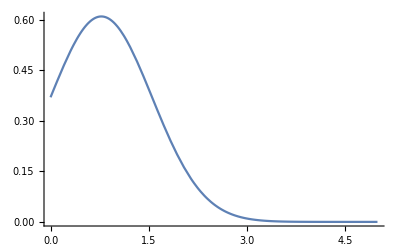

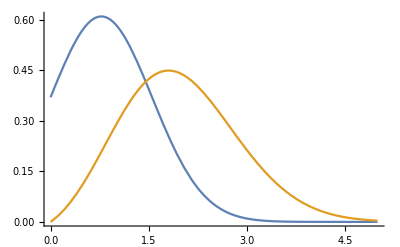

```mathematica
Plot[{f1[x]},{x,0,5},PlotRange->All]
Plot[{f1[x],f2[x]},{x,0,5},PlotRange->All]
Plot[{f1[x],f2[x],f3[x]},{x,0,5},PlotRange->All]

Plot[{f1[x],f2[x],f3[x]},{x,0,5},
PlotRange->{{0,5},{0,0.7}},
Frame->True,
Filling->Axis,
PlotStyle->{Gray,Red,Blue,Green,Magenta},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic
]
```

```mathematica
f2[x]
```

If[0≤x<2,x/4,If[2≤x<4,1-x/4,0]]

```mathematica
f3[x]
```

If[0≤x<2,x^2/16,If[2≤x<4,1/16 (4-(x-2)^2)+1/2 (x-x^2/8-(2-2^2/8)),If[4≤x<6,1/2 ((4-4^2/8)-(x-2-1/8 (x-2)^2)),0]]]

```mathematica
f3[2.]
```

```mathematica
∫_-3.^2. If[y3≤0,0.,gauss[y3,mu,sig]/n1] ∫_(-3.-y3)^(2.-y3) If[y2≤0,0.,gauss[y2,mu,sig]/n1] If[2.-y2-y3≤0,0.,gauss[2.-y2-y3,mu,sig]/n1]ⅆy2ⅆy3
```

Integrate::intnest: The integral ∫_(-3.-y3)^(2.-y3) If[y2≤0,0.,gauss[y2,mu,sig]/n1]If[2.-y2-y3≤0,0.,gauss[2.-y2-y3,mu,sig]/n1]ⅆy2ⅆy3 cannot be interpreted. The number of definite and indefinite integral operators must match the number of differential operators.

```mathematica
g1[x1_]:=gauss[x1,mu,sig]/n1;
g2[x2_]:=Integrate[g1[y2] g1[x2-y2],{y2,x2-5,x2}];
g3[x3_]:=NIntegrate[g1[y3] Integrate[g1[y2] g1[x3-y3-y2],{y2,x3-y3-5,x3-y3}],{y3,0,5.}   ];
g1[x]
g2[x]
g3[x]
g3[2.]
```

0.610542 ⅇ^(-0.828952 (-0.776641+x)^2)

0.0943849 ⅇ^((1.2876-0.414476 x) x) (1. Erf[6.43798-0.643798 x]+1. Erf[0.+0.643798 x])

∫_(-5+x)^x 0.0576259 ⅇ^(-0.414476 x^2+x (1.2876+0.828952 y3)-0.828952 (-0.776641+y3)^2+(-1.2876-0.414476 y3) y3) (1. Erf[0.+0.643798 x-0.643798 y3]+1. Erf[6.43798-0.643798 x+0.643798 y3])ⅆy3

```mathematica
g3[2.]
```

∫_-3.^2. 0.144209 2.71828^((0.370308-0.414476 y3) y3) ⅇ^(-0.828952 (-0.776641+y3)^2) (1. Erf[1.2876-0.643798 y3]+1. Erf[5.15038+0.643798 y3])ⅆy3

```mathematica
Plot[{g1[x],g2[x],g3[x]},{x,0,5},
PlotRange->{{0,5},{0,0.7}},
Frame->True,
Filling->Axis,
PlotStyle->{Gray,Red,Blue,Green,Magenta},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic
]
```

$Aborted

```mathematica
g3[2.]
```

∫_-3.^2. 0.144209 2.71828^((0.370308-0.414476 y3) y3) ⅇ^(-0.828952 (-0.776641+y3)^2) (1. Erf[1.2876-0.643798 y3]+1. Erf[5.15038+0.643798 y3])ⅆy3

```mathematica
Erf[1.]
```

0.842701

```mathematica
1+1
```